```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files

## Importing data

```mathematica
(*numerical solution, flag == 0,
 exact solution, flag == 1 and 
error flag == 2
error velocity space flag == 3
fe index distribution flag == 4
convergence table flag == 5*)
importdata[dof_,p_,refinetype_,flag_,outputdir_]:=Module[{result,filename},
Which[flag == 0,
filename=StringJoin["../",outputdir,"/solution/numerical_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],

flag == 1,
filename=StringJoin["../",outputdir,"/solution/exact_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],

flag == 2,
filename=StringJoin["../",outputdir,"/solution/error",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 3,
filename=StringJoin["../",outputdir,"/solution/error_velocity_space",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 4,
filename=StringJoin["../",outputdir,"/solution/fe_index",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 5,
filename=StringJoin["../",outputdir,"/convergence_tables/convergence_table",refinetype,"degree_",ToString[p]]
];

result = Import[filename,"Table"][[2;;-1,All]]
]
```

## IDs for different variables

```mathematica
(*we declare the IDs for different variables, this will help us with plotting*)
IDSpace = 1;
IDRho = 1+IDSpace;
IDvx = 2+IDSpace;
IDtheta = 3+IDSpace;
```

## Mapping to Primitive variables

```mathematica
(*we change the numerical solution obtained to the primitive variables.*)
ConvToPrim[sol_]:=Module[{factorθ,factorσ,factorq,trialsol},
trialsol = sol;
factorθ = √2;
trialsol⟦All,IDtheta⟧ =factorθ * sol⟦All,IDtheta⟧;

trialsol
]
```

## Poisson Heat conduction

### G20

```mathematica
ndof=3072;
foldername = "Tests/build/output_N6_poisson_heat_1D_Kn0p1";
sol=importdata[ndof,1,"_global_",0,foldername];
sol = ConvToPrim[sol];
```

#### θ

```mathematica
plot1=ListPlot[Error20⟦All,{1,IDtheta}⟧,Joined->True];
```

### G26

```mathematica
ndof=4096;
foldername = "Tests/build/output_N8_poisson_heat_1D_Kn0p1";
sol26=importdata[ndof,1,"_global_",0,foldername];
sol26 = ConvToPrim[sol26];
```

#### θ

```mathematica
plot1=ListPlot[Error20⟦All,{1,IDtheta}⟧,Joined->True];
```

### Error G20 and G26

```mathematica
ErrorG20G26 = ConstantArray[0,{Length[sol],2}];
Table[ErrorG20G26⟦ii⟧={sol⟦ii,1⟧,Abs[sol⟦ii,IDtheta⟧-sol26⟦ii,IDtheta⟧]},{ii,1,Length[sol]}];
```

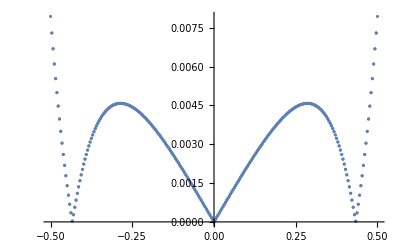

```mathematica
ListPlot[ErrorG20G26]
```

### M Adaptive

#### convergenceTable(N6N8, equilibrium deviation based)

```mathematica
ndof=3072;
foldername = "Results/Results_Poisson_1D_m_adaptive/output_N6_N8_poisson_heat_1D_Kn0p1";

ConvTable=importdata[ndof,1,"_global_",5,foldername];

(*extract the appropriate values*)
RemoveIndices = Range[3,Length[ConvTable],2];
Do[RemoveIndices⟦ii⟧={RemoveIndices⟦ii⟧},{ii,1,Length[RemoveIndices]}];
ConvTable=Delete[ConvTable,RemoveIndices]⟦All,{5,1}⟧;
ConvTableUniformN6N8 = {ConvTable⟦1⟧,ConvTable⟦-1⟧};
```

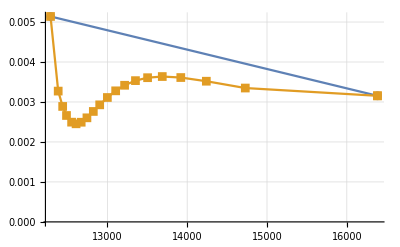

```mathematica
ListPlot[{ConvTableUniformN6N8,ConvTable},Joined->True,PlotMarkers->Automatic,GridLines->Automatic]
```

#### convergenceTable(N6N8N12,equilibrium deviation based)

```mathematica
ndof=3072;
foldername = "Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_poisson_heat_1D_Kn0p1";

ConvTable=importdata[ndof,1,"_global_",5,foldername];

(*extract the appropriate values*)
RemoveIndices = Range[3,Length[ConvTable],2];
Do[RemoveIndices⟦ii⟧={RemoveIndices⟦ii⟧},{ii,1,Length[RemoveIndices]}];
ConvTable=Delete[ConvTable,RemoveIndices]⟦All,{5,1}⟧;
ConvTableUniformN6N8N12 = {ConvTable⟦1⟧,ConvTable⟦-1⟧};
```

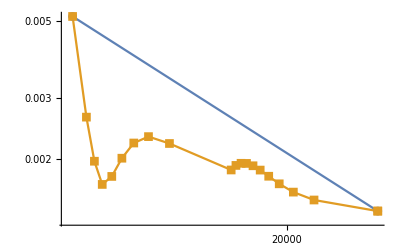

```mathematica
ListLogLogPlot[{ConvTableUniformN6N8N12,ConvTable},Joined->True,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->Full]
```

#### convergenceTable(N6N8N12N14,equilibrium deviation based)

```mathematica
ndof=3072;
foldername = "Results/Results_Poisson_1D_m_adaptive/output_N6_N8_N12_N14_poisson_heat_1D_Kn0p1";

ConvTable=importdata[ndof,1,"_global_",5,foldername];

(*extract the appropriate values*)
RemoveIndices = Range[3,Length[ConvTable],2];
Do[RemoveIndices⟦ii⟧={RemoveIndices⟦ii⟧},{ii,1,Length[RemoveIndices]}];
ConvTable=Delete[ConvTable,RemoveIndices]⟦All,{5,1}⟧;
ConvTableUniformN6N8N12N14 = {ConvTable⟦1⟧,ConvTable⟦-1⟧};
```

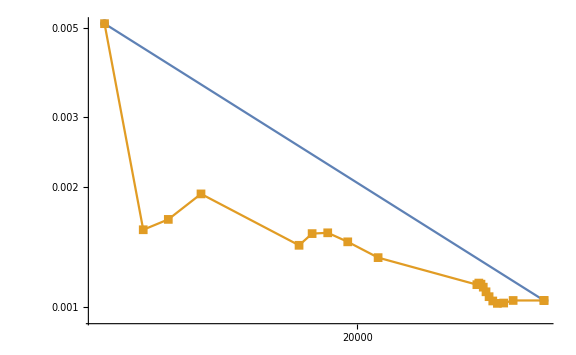

```mathematica
ListLogLogPlot[{ConvTableUniformN6N8N12N14,ConvTable},Joined->True,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->Full,ImageSize->Large]
```

```mathematica
?PlotRange
```

PlotRange is an option for graphics functions that specifies what range of coordinates to include in a plot.

#### convergenceTable(N6N8, center distance based)

```mathematica
ndof=3072;
foldername = "Results/Results_Poisson_1D_m_adaptive/distance_center_based/output_N6_N8_poisson_heat_1D_Kn0p1";

ConvTable=importdata[ndof,1,"_global_",5,foldername];

(*extract the appropriate values*)
RemoveIndices = Range[3,Length[ConvTable],2];
Do[RemoveIndices⟦ii⟧={RemoveIndices⟦ii⟧},{ii,1,Length[RemoveIndices]}];
ConvTable=Delete[ConvTable,RemoveIndices]⟦All,{5,1}⟧;
ConvTableUniformN6N8 = {ConvTable⟦1⟧,ConvTable⟦-1⟧};
```

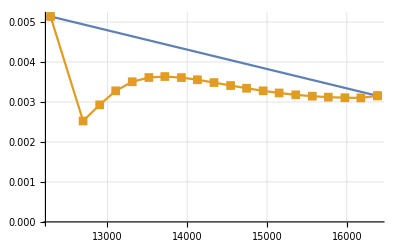

```mathematica
ListPlot[{ConvTableUniformN6N8,ConvTable},Joined->True,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->Full]
```

#### convergenceTable(N6N8N12,center distance based)

```mathematica
ndof=3072;
foldername = "Results/Results_Poisson_1D_m_adaptive/distance_center_based/output_N6_N8_N12_poisson_heat_1D_Kn0p1";

ConvTable=importdata[ndof,1,"_global_",5,foldername];

(*extract the appropriate values*)
RemoveIndices = Range[3,Length[ConvTable],2];
Do[RemoveIndices⟦ii⟧={RemoveIndices⟦ii⟧},{ii,1,Length[RemoveIndices]}];
ConvTable=Delete[ConvTable,RemoveIndices]⟦All,{5,1}⟧;
ConvTableUniformN6N8N12 = {ConvTable⟦1⟧,ConvTable⟦-1⟧};
```

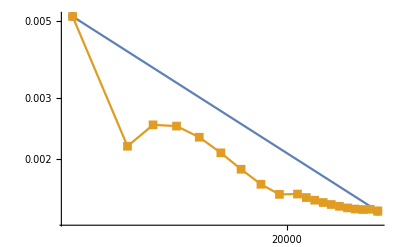

```mathematica
ListLogLogPlot[{ConvTableUniformN6N8N12,ConvTable},Joined->True,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->Full]
```

#### convergenceTable(N6N8N12N14,center distance based)

```mathematica
ndof=3072;
foldername = "Results/Results_Poisson_1D_m_adaptive/distance_center_based/output_N6_N8_N12_N14_poisson_heat_1D_Kn0p1";

ConvTable=importdata[ndof,1,"_global_",5,foldername];

(*extract the appropriate values*)
RemoveIndices = Range[3,Length[ConvTable],2];
Do[RemoveIndices⟦ii⟧={RemoveIndices⟦ii⟧},{ii,1,Length[RemoveIndices]}];
ConvTable=Delete[ConvTable,RemoveIndices]⟦All,{5,1}⟧;
ConvTableUniformN6N8N12N14 = {ConvTable⟦1⟧,ConvTable⟦-1⟧};
```

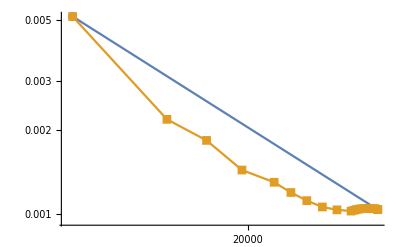

```mathematica
ListLogLogPlot[{ConvTableUniformN6N8N12N14,ConvTable},Joined->True,PlotMarkers->Automatic,GridLines->Automatic,PlotRange->Full]
```